```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,4000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

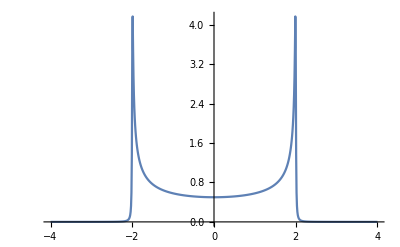

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0][[1,1]]]},{ω,Range[-4,4,0.01]}],PlotRange->All]
```

```mathematica
Il1:=Inverse[IdentityMatrix[1]-sl7.T1[1].SR[ω,0.001,1,0].T1[1]].sl7;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T1[1].sl7.T1[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:= Inverse[(ω+ⅈ*δ-ϵ1)IdentityMatrix[1]]
```

```mathematica
leftlead[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1],imp=imp[ω,δ,t,ϵ,ϵ1]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,RandomInteger[{1,20}]]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,RandomInteger[{1,20}]]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,RandomInteger[{1,20}]]; J=J];sl6=Inverse[IdentityMatrix[1]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,RandomInteger[{1,20}]]; J=J]]
```

```mathematica
ll[ω_,ϵ1_]:=Mean[Table[leftlead[0,0.001,1,0,ϵ1],10000]]
```

```mathematica
tr[ω_,δ_,ϵ1_]:=Module[{sl17=ll[ω,ϵ1]},Il1:=Inverse[IdentityMatrix[1]-sl7.T1[1].SR[ω,0.001,1,0].T1[1]].sl7;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T1[1].sl7.T1[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
Table[{ω,tr[ω,0.001,0]},{ω,Range[0,3,0.01]}]
```

{{0.,1.},{0.01,0.999978},{0.02,0.999959},{0.03,0.999943},{0.04,0.999898},{0.05,0.999826},{0.06,0.999756},{0.07,0.999673},{0.08,0.999577},{0.09,0.999484},{0.1,0.999348},{0.11,0.999229},{0.12,0.999082},{0.13,0.998922},{0.14,0.998734},{0.15,0.998564},{0.16,0.998366},{0.17,0.998139},{0.18,0.99793},{0.19,0.997692},{0.2,0.997427},{0.21,0.997178},{0.22,0.996887},{0.23,0.996597},{0.24,0.996293},{0.25,0.995977},{0.26,0.995662},{0.27,0.995303},{0.28,0.994947},{0.29,0.994577},{0.3,0.994193},{0.31,0.99381},{0.32,0.993385},{0.33,0.99296},{0.34,0.992536},{0.35,0.992083},{0.36,0.991602},{0.37,0.991136},{0.38,0.990628},{0.39,0.990133},{0.4,0.98961},{0.41,0.989072},{0.42,0.98852},{0.43,0.98794},{0.44,0.987359},{0.45,0.986777},{0.46,0.986153},{0.47,0.985541},{0.48,0.984887},{0.49,0.984245},{0.5,0.983561},{0.51,0.982888},{0.52,0.982186},{0.53,0.981456},{0.54,0.980723},{0.55,0.979987},{0.56,0.979209},{0.57,0.978441},{0.58,0.977631},{0.59,0.976817},{0.6,0.975999},{0.61,0.975152},{0.62,0.974276},{0.63,0.973396},{0.64,0.972497},{0.65,0.971582},{0.66,0.970649},{0.67,0.969699},{0.68,0.968741},{0.69,0.967755},{0.7,0.96675},{0.71,0.965715},{0.72,0.964684},{0.73,0.963613},{0.74,0.962543},{0.75,0.961444},{0.76,0.960325},{0.77,0.959176},{0.78,0.958018},{0.79,0.956849},{0.8,0.95565},{0.81,0.954429},{0.82,0.953188},{0.83,0.951916},{0.84,0.950632},{0.85,0.949327},{0.86,0.948008},{0.87,0.946649},{0.88,0.945284},{0.89,0.943887},{0.9,0.942468},{0.91,0.941016},{0.92,0.939557},{0.93,0.938057},{0.94,0.93654},{0.95,0.935006},{0.96,0.933431},{0.97,0.931837},{0.98,0.930217},{0.99,0.92857},{1.,0.926896},{1.01,0.925194},{1.02,0.923464},{1.03,0.921712},{1.04,0.919923},{1.05,0.918106},{1.06,0.916258},{1.07,0.914374},{1.08,0.912465},{1.09,0.910523},{1.1,0.908549},{1.11,0.906542},{1.12,0.904505},{1.13,0.902429},{1.14,0.900315},{1.15,0.898169},{1.16,0.895989},{1.17,0.893767},{1.18,0.891511},{1.19,0.889214},{1.2,0.886878},{1.21,0.8845},{1.22,0.882081},{1.23,0.879622},{1.24,0.877118},{1.25,0.87457},{1.26,0.871976},{1.27,0.869336},{1.28,0.866649},{1.29,0.863913},{1.3,0.861128},{1.31,0.858292},{1.32,0.855401},{1.33,0.85246},{1.34,0.849461},{1.35,0.846407},{1.36,0.843294},{1.37,0.840122},{1.38,0.836888},{1.39,0.83359},{1.4,0.830223},{1.41,0.826799},{1.42,0.8233},{1.43,0.819731},{1.44,0.816082},{1.45,0.81237},{1.46,0.808574},{1.47,0.80469},{1.48,0.800729},{1.49,0.796683},{1.5,0.792556},{1.51,0.788319},{1.52,0.783996},{1.53,0.779574},{1.54,0.775059},{1.55,0.770416},{1.56,0.765685},{1.57,0.760815},{1.58,0.75585},{1.59,0.750734},{1.6,0.745501},{1.61,0.740131},{1.62,0.734619},{1.63,0.728958},{1.64,0.723157},{1.65,0.717161},{1.66,0.711027},{1.67,0.704696},{1.68,0.698155},{1.69,0.691453},{1.7,0.684521},{1.71,0.677343},{1.72,0.669971},{1.73,0.662304},{1.74,0.654415},{1.75,0.646218},{1.76,0.637716},{1.77,0.628862},{1.78,0.619709},{1.79,0.610152},{1.8,0.600156},{1.81,0.589777},{1.82,0.578885},{1.83,0.567466},{1.84,0.555432},{1.85,0.542789},{1.86,0.529434},{1.87,0.515319},{1.88,0.500229},{1.89,0.484193},{1.9,0.466941},{1.91,0.448275},{1.92,0.428079},{1.93,0.405845},{1.94,0.381317},{1.95,0.353665},{1.96,0.322104},{1.97,0.285165},{1.98,0.240274},{1.99,0.183605},{2.,0.117},{2.01,0.0716751},{2.02,0.0510423},{2.03,0.0401601},{2.04,0.0334208},{2.05,0.0287125},{2.06,0.0251748},{2.07,0.0224738},{2.08,0.0203556},{2.09,0.0185714},{2.1,0.0170746},{2.11,0.0157543},{2.12,0.0146927},{2.13,0.0137275},{2.14,0.0128362},{2.15,0.0121176},{2.16,0.0114381},{2.17,0.0108262},{2.18,0.0102709},{2.19,0.00973119},{2.2,0.00930281},{2.21,0.00884556},{2.22,0.0084546},{2.23,0.00812405},{2.24,0.00775792},{2.25,0.00744611},{2.26,0.00715531},{2.27,0.00688344},{2.28,0.00665659},{2.29,0.0064172},{2.3,0.00616549},{2.31,0.00597981},{2.32,0.00577923},{2.33,0.00556544},{2.34,0.00541156},{2.35,0.00521782},{2.36,0.00508037},{2.37,0.00492739},{2.38,0.00478203},{2.39,0.00462175},{2.4,0.00449009},{2.41,0.00438536},{2.42,0.00426512},{2.43,0.00414974},{2.44,0.00403988},{2.45,0.00393427},{2.46,0.00383333},{2.47,0.00371763},{2.48,0.0036433},{2.49,0.0035539},{2.5,0.00346833},{2.51,0.00336801},{2.52,0.00330612},{2.53,0.00322973},{2.54,0.00315591},{2.55,0.00308456},{2.56,0.00301604},{2.57,0.00293398},{2.58,0.00288593},{2.59,0.00280883},{2.6,0.00276471},{2.61,0.0027069},{2.62,0.00263645},{2.63,0.00258262},{2.64,0.0025447},{2.65,0.00248014},{2.66,0.00243138},{2.67,0.00238386},{2.68,0.00233787},{2.69,0.0023065},{2.7,0.00224986},{2.71,0.00220802},{2.72,0.00217987},{2.73,0.00212758},{2.74,0.00210143},{2.75,0.00205157},{2.76,0.00201526},{2.77,0.00199181},{2.78,0.00195712},{2.79,0.001912},{2.8,0.00189069},{2.81,0.00185887},{2.82,0.00181663},{2.83,0.00178653},{2.84,0.001768},{2.85,0.00173908},{2.86,0.00171112},{2.87,0.00167342},{2.88,0.00165721},{2.89,0.00162093},{2.9,0.00160568},{2.91,0.00158099},{2.92,0.00154701},{2.93,0.00153304},{2.94,0.00151004},{2.95,0.00147802},{2.96,0.00145617},{2.97,0.00144396},{2.98,0.00142282},{2.99,0.00140236},{3.,0.00138215}}

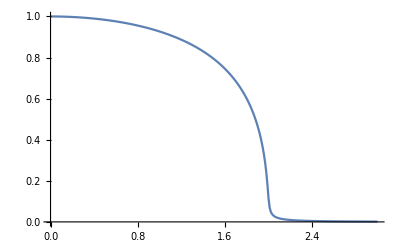

```mathematica
ListPlot[%32,Joined->True]
```